# An introduction to Mathematica

## Tutorial, Version 1 (5 September 2012)

by Flip Tanedo (pt267@cornell.edu)
Prepared for the the students of Physics 3327 (Advanced Electricity & Magnetism) at Cornell University, Fall 2012

This is a short tutorial to introduce you to the Mathematica computer algebra system. This document was prepared in Mathematica 8.1 and is based largely on the Mathematica 8 Virtual Book.

I may update this document this with additional examples as necessary.

## What is Mathematica?

Mathematica is a widely used computer algebra system, which means that it can do symbolic calculations and do nifty things like evaluate integrals analytically. In this way it differs from numerical computational software like MATLAB. Mathematica is a versatile program which can be used for a range of applications; in this tutorial we’ll focus on the basics---which have been enough to get me through a Ph.D in theoretical physics.

### Why should I use Mathematica?

Mathematica is a powerful tool to add to your physics arsenal. It allows you to do calculations quickly so that you can focus on the physics of a problem. In the old days, physicisits had to go to tables of integrals (Gradshteyn and Ryzhik) to do integrals---Mathematica spares you from this pain.

More than this, Mathematica provides tools that can be applies to a broad range of topics. Try checking out: http://playingwithmathematica.com
http://www.wolfram.com/products/webmathematica/examples/examples.html

### Now that I have Mathematica, I don’t need to learn any math, right?

Nice try, but like any tool, Mathematica is only as intelligent as its user. Mathematica lots you to cut out a lot of the intermediate steps in tedious calculations, preventing sloppy errors and saving time. However, it’s up to the user to know what calculations need to be done. For this, you need to actually know and understand mathematics and physics.

### Is there an open source alternative?

The short answer is: not really. Mathematica is a commercial program and while the physics community tends towards open source, you’ll be hard pressed to find an open source alternative with the same functionality. 

While Mathematica does cost quite a bit, the student version is signficantly discounted. (If you intend on continuing in physics, I suggest getting a permanent license rather than the one-semester license.) It’s still not cheap, but it’s a reasonable investment. Fortunately, many of the Mathematica-based programs that one uses in research are available for free.

For Physics 3327 (Fall 2012): you are welcome to use an open source computer algebra system as an alternative to Mathematica, but you’ll be on your own to get things to work. In a pinch, you can also probably get some pretty good mileage out of Wolfram Alpha, but at the moment it is not a suitable replacement for Mathematica.

## How to learn how to use Mathematica

The first thing you need to know is where to find help. There are two important things to note: (1) don’t e-mail me and (2) the Mathematica help documentation is fantastic. 

From Mathematica, go to Help > Virtual Book to access the Mathematica book. Back in the old days graduate students actually bought this book to have a reference while using Mathematica. Fortunately for you, the entire volume is available from the Help menu. Go ahead and check this out to see what’s available. You might want to skim over the Introduction to get a feel for what’s in here. Most of the examples that we’ll be going through come from the Mathematica Virtual Book.

Another useful reference from the Help menu is Help > Documentation Center. The topics presented here are similar to those in the virtual book, but are arranged to be more useful as a quick reference. More importantly, you can use the search menu here when you don’t know what to do.

As a quick exercise, go ahead and use the Documentation Center to look up “Bessel functions” and look at the output. In addition to describing built-in implementations of the various individual Bessel functions, the search results also yield Mathematica guides which provide a broader description of how Bessel functions are implemented.

Here’s a useful trick: sometimes you’ll be looking at Mathematica code and you’ll have no idea what a particular command is doing. You can right-click to get a menu and select “Get Help” to pull up the Mathematica documentation on that function. As an example, here’s the implementation of e, the base of the natural logarithm:

```mathematica
ⅇ
```

ⅇ

Go ahead and right click it and select “Get Help.” The Documentation Center pops up and tells you about this this character.

## Structure

### Notebook make your life easier

The heart of Mathematica is its kernel, this is the workhorse that is actually doing your intergrals. It is fed commands (things to evaluate, definitions of variables, replacement rules) and it outputs the result of these commands to the screen. One thing to remember: the kernel remembers the things that you feed it; if you define a variable x to take a value 25, then it will apply this definition to every subsequent instance of x. 

The kernel, however, is not particularly user friendly, and for the most part we would rather not deal with it directly. Instead, we work withnotebooks. This file is an example of a Mathematica notebook.

### Notebooks are divided into cells

A notebook is divided into cells, which are indicated by the vertical blue brackets on the right. So far most of the cells in this document have been plain text---this is nice for commentary, but not particularly useful. More common are input cells that can send commands to the kernel and ask it to do stuff. For example, here’s a “hello world” cell, which we’ll work with in the next section:

```mathematica
1+1
```

2

You can start a new cell by clicking in between cells (or pressing the down arrow).  

There are other types of cells. For example, this cell is a text cell. These don’t do much, but they sure are useful for documenting your code. When you make a new cell, you can pick the cell type from the menu bar: Format > Style. New cells default to input cells.

And there you go, now you can start running

## Simple Tasks

### The ‘hello world’ of Mathematica: how to evaluate an expression

Let’s go back to a simple ‘hello world’ calculation:

```mathematica
1+1
```

This is an input cell that is asking for the sum of one plus one. This cell is just sitting with a command waiting to be sent to the kernel. To do this, place the cursor in the cell and press [shift] + [return]. The cell should now look like this:

```mathematica
1+1
```

2

Inputting [shift] + [return] this sends the command to the kernel, indicated by the In[n]:= label, which tells you that it is the nth request sent to the current kernel. The kernel’s response is outputted just below with a Out[n]:= label. Alright, we’ve done the hard part! For the rest of this document it’ll be up to you to [shift]+[return] through the document to see what various commands do.

### Parentheses

Mathematica also knows about order of operations.

```mathematica
4+4 2
(4+4)2
```

12

16

Note that you are only allowed to use parenthesis... no curly braces, no brackets, nothing else: those have different uses in Mathematica.

### I don’t know how to type that in... how do I do it?

Mathematica has a few useful GUI palettes for inputting expressions. I like to leave the “Basic Math Assistnat” up: from the menu bar, Palettes > Basic Math Assistant. Go ahead and enter a few simple expressions. I’ll get you started:

```mathematica
5^2
√25
(* by the way, you can place comments in between a "parenthesis-asterisk" pair *)
```

25

5

### Variables

It’s easy to work with variables. For example, we can add two polynomial expressions:

```mathematica
3 x^2+4 x^2
```

7 x^2

Now let’s see how to assign values to variables... it’s actually exactly what you’d expect:

```mathematica
x=3
x^2+2
```

3

11

Great! We’ve now fixed the variable x. In fact, x has now been set in the kernel and any subsequent command which includes x will automatically make the replacement x=3. Try this for yourself: go back to the previous input, 3 x^2+4 x^2, and evaluate it. Note that it no longer returns 7 x^2, but instaed 63. This can sometimes be a little annoying.

### Clearing Variables

If you want to return x to an empty variable which can be manipulated analytically, you can use the following command:

```mathematica
Clear[x]
x
```

x

... where we have checked that indeed, x does not return a numerical value. But this is tedious to do for each variable to which you may have assigned a value in your Notebook. A more useful command clears all definitions in the kernel:

```mathematica
ClearAll["Global`*"]
```

This is equivalent to restarting the kernel, which you can do manually from the Evaluation menu.

### Remarks: how to pull the plug

If you ever get in trouble and the Mathematica kernel is stuck doing a long calculation, you can either wait for Mathematica to give up after it senses non-convergence or you can force quit the kernel from the menu bar: Evaluation > Abort Evaluation.

### Example: converting mass to energy

In the non-relativistic limit (i.e. neglecting kinetic energy) the total energy of an object is equal to its rest mass times a conversion factor, the speed of light squared. Here we’ll demonstrate how to do this conversion and we’ll even throw in SI units, which we write as variables.

```mathematica
c=3 10^8 meters/seconds; (* this semi-colon suppresses the output, but the command still goes to the kernel *)

m = 1.5 kilograms;
energy = m c^2
```

(1.35×10^17 kilograms meters^2)/seconds^2

What if we instead wanted to use Imperial units? Here’s one clunky way of doing it. We’ll see a slicker way below.

```mathematica
kilograms = 2.20462 pounds;
meters = 3.28084 feet;
energy
```

(3.2036×10^18 feet^2 pounds)/seconds^2

Just to keep things tidy, let’s clear everything once again.

```mathematica
ClearAll["Global`*"]
```

## Functions and plotting: a first pass

### A function of one variable

Now suppose we wanted to be able to calculate the energy as a function of an input mass? For this we define a function as follows:

```mathematica
Energy[inputMass_]:= inputMass c^2
```

Note that the argument of the function is written in square brackets immediately after the function name. The function is defined with a colon and equal sign. To help keep everything clear, Mathematica automatically italicizes (and green-ifies) input variable names on the right hand side of the function definition. 

By the way, note that we haven’t defined the speed of light since our last Clear All. Let’s do that now:

```mathematica
c=3 10^8 meters/seconds;
```

Now we can find the energy for various masses:

```mathematica
Energy[1.3 kilograms]
Energy[10 kilograms]
```

(1.17×10^17 kilograms meters^2)/seconds^2

(900000000000000000 kilograms meters^2)/seconds^2

### A function of two variables

You might know that this expression for the energy of an object is only valid in the non-relativistic limit. The full relativistic energy also includes the contribution from kinetic energy which is added to the rest mass energy in quadrature. To show this, we can define a function that takes in two arguments:

```mathematica
FullEnergy[restMass_,momentum_]:= √(restMass^2 c^4+momentum^2 c^2)
```

Let’s test it:

```mathematica
FullEnergy[2.8 kilograms, 1.8 10^8 kilograms meters/seconds]
```

2.57721×10^17 √((kilograms^2 meters^4)/seconds^4)

That’s kind of clunky. Mathematica doesn’t want to simplify the square root because it doesn’t know what kind of numbers are inside. As homework you can figure out how to tell Mathematica that it should assume that “kilograms”, “meters”, and “seconds” are real numbers. Hint: look up assumptions in the documentation.

### Plotting functions

One very useful thing to be able to do is to make plots. Here’s a good example:

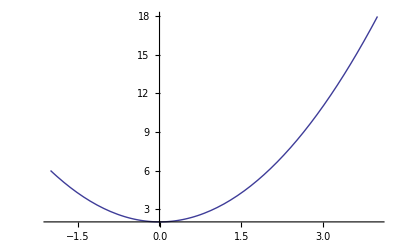

```mathematica
Plot[x^2+2,{x,-2,4}]
```

If you have a function defined, you can plot it as follows:

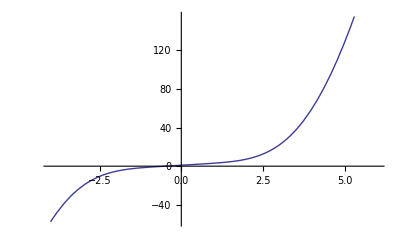

```mathematica
myFunction[x_]=x^3+2x Cos[x]+1;
Plot[myFunction[z],{z,-4,6}]
```

### Fancier plots

Here’s a 3d plot of the Higgs boson potential. Note that you can rotate the 3D plot.

```mathematica
Plot3D[(x^2+y^2-90)^2,{x,-12,12},{y,-12,12}]
```

-Graphics3D-

Here are what the contours look like:

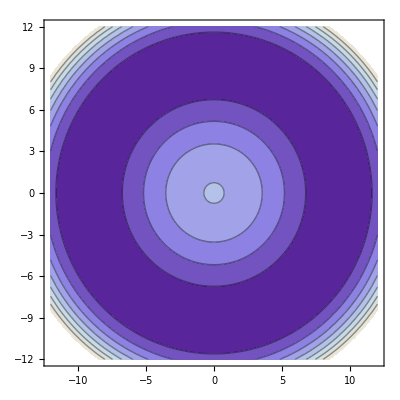

```mathematica
ContourPlot[(x^2+y^2-90)^2,{x,-12,12},{y,-12,12}]
```

## Lists

### Curly braces are lists

One thing you might have noticed from the plotting examples above that we have started using curly braces. These are used by Mathematica to store lists. In the plots above, the lists took the form: {variable name, minimum value, maximum value}. But more generally, you can do a lot with a list. For example, you can apply a function to a list to get a list of results:

```mathematica
arbitraryFunction[x_]=1/x;
arbitraryFunction[{1,2,3,4,9.2}]
```

{1,1/2,1/3,1/4,0.108696}

Note that Mathematica gives fractional outputs unless you feed it a decimal point.

### For more about lists, see the documentation

Lists are a pretty powerful tool in Mathematica. I’ll leave you to read about them more on your own.

## Calculus

Here it’s just easiest to throw out a bunch of examples.

### Derivatives

```mathematica
D[( x^2+3x), x]
```

3+2 x

```mathematica
D[( y x^2+3w), x]
```

2 x y

```mathematica
D[x^2+3x,x] (* alternate, clunkier notation *)
```

3+2 x

```mathematica
D[x^2+3x,{x,2}] (* second derivative w/rt x *)
```

2

```mathematica
D[x^n,{x,1}]
```

n x^(-1+n)

### Integrals

```mathematica
∫x^3 ⅆx
```

x^4/4

```mathematica
∫_0^2 x^3 ⅆx
```

4

```mathematica
∫_2^t (x^2+3x)ⅆx
```

-26/3+(3 t^2)/2+t^3/3

## Vectors as lists

### Defining a vector as a list and picking elements of the vector

```mathematica
v={3,5,6};
v[[2]]
```

5

```mathematica
w={1,2,3,4,5,6,7};
w[[6]]
```

6

### Vector arithmetic

```mathematica
v={5,3,2};
w={1,7,9};
v+w
```

{6,10,11}

### Vector product

Be careful, note that the “matrix multiplication” of vectors is performed using a period. Without the period you get something totally different!

```mathematica
v v
```

{25,9,4}

```mathematica
v.v
```

38

### Matrices

These are easiest to use using the Basic Math Palette:

```mathematica
R=({{Cos[π/4], -Sin[π/4]}, {Sin[π/4], Cos[π/4]}});
v={1,0};
R.v
```

{1/(√2),1/(√2)}

And let’s see how the matrix looks if we didn’t use the pretty formatting:

```mathematica
R
```

{{1/(√2),-1/(√2)},{1/(√2),1/(√2)}}

### Homework: Defining 3x3 matrices

Hint: check out the Insert menu if you want to have the ‘pretty’ matrix. Or write the matrix as a list of lists.

## Algebra

As homework, you can figure out how to expand polynomials, simplify complicated (and “FullSimplify”) expressions.

## Functions: Rules & Patterns

### Postfix

You can append operations after an expression with //, this will apply the operation to the expression. Here’s an example using Euler’s Γ function.

```mathematica
x Gamma[x]//FullSimplify
```

Gamma[1+x]

### Replacement rules (->)

Sometimes you have an expression that you want to evaluate with specific values, you can use a replacement rule. This is usually appended after an expression using slash dot. The replacement rules are written using a hyphen and a greater-than symbol.

```mathematica
{x,x^2,a,b}/.x->3
```

{3,9,a,b}

Multiple replacements:

```mathematica
{x,x^2,a,b}/.{x->3,a->2}
```

{3,9,2,b}

This is useful as it only applies to the one instance:

```mathematica
myVelocity=5 meters/seconds;
myVelocity /.{meters->3.281 feet}
myVelocity
```

(16.405 feet)/seconds

(5 meters)/seconds

Note how the value of myVelocity was not overwritten by the replacement rule.

### Set delayed (:=)

You already know how the equal sign works. What about the := that we use when defining functions? This is called teh set delayed operation. While = will evaluate both sides of the operator and set the left-hand side to be the right-hand side, set delayed (:=) will not evaluate the right-hand side until after it has replaced the left-hand side. As such, it is evaluated ‘fresh’ each time it is called.

This is somewhat abstract... see the description for rule delayed below for more intuition. Meanwhile, here’s a neat example of a recursively defined expression for the Fibonacci sequence:

```mathematica
Clear[fib]
fib[1]=fib[2]=1;
fib[n_]:=fib[n]=fib[n-1]+fib[n-2]
fib[5]
Definition[fib]
```

5

fib[1]=1
 
fib[2]=1
 
fib[3]=2
 
fib[4]=3
 
fib[5]=5
 
fib[n_]:=fib[n]=fib[n-1]+fib[n-2]

### Rule delayed (:>)

Like set delayed. This is a replacement rule that doesn’t evaluate the replacement until it actually replaces something.

```mathematica
{x,x,x}/.x:>RandomReal[]
```

{0.0709285,0.197683,0.585661}

Compare this to:

```mathematica
{x,x,x}/.x->RandomReal[]
```

{0.511842,0.511842,0.511842}

## Plotting: making everything pretty

Here are some demonstrations of useful options for the plot command to make your plots a bit nicer. As always, see the documentation for more options. These examples are mostly from the tutorial, http://reference.wolfram.com/mathematica/tutorial/Options.html.

### Labeling axes

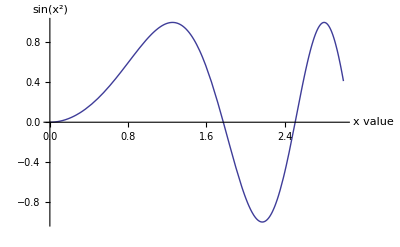

```mathematica
Plot[Sin[x^2],{x,0,3},AxesLabel->{"x value",Sin[x^2]}]
```

### Restricting the range

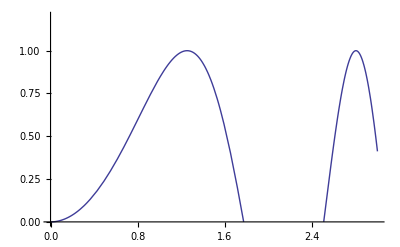

```mathematica
Plot[Sin[x^2],{x,0,3},PlotRange->{0,1.2}]
```

### Fancy lines

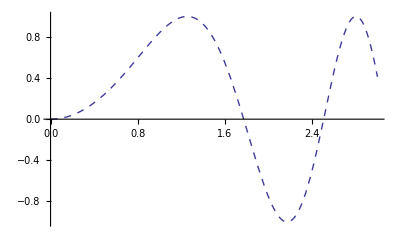

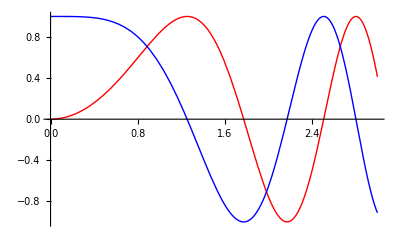

```mathematica
Plot[Sin[x^2],{x,0,3},PlotStyle->Dashed]
Plot[{Sin[x^2],Cos[x^2]},{x,0,3},PlotStyle->{Red,{Blue,Thick}}]
```

### Contour Plots

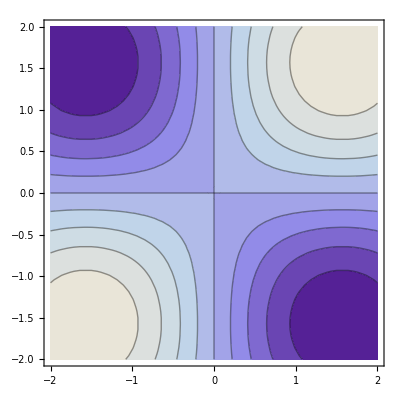

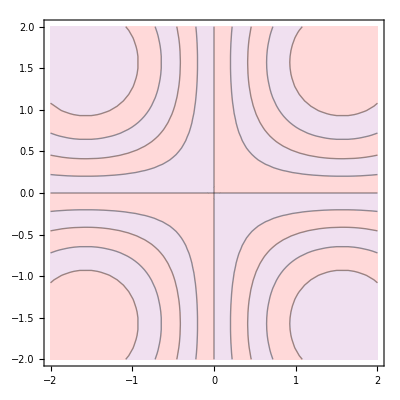

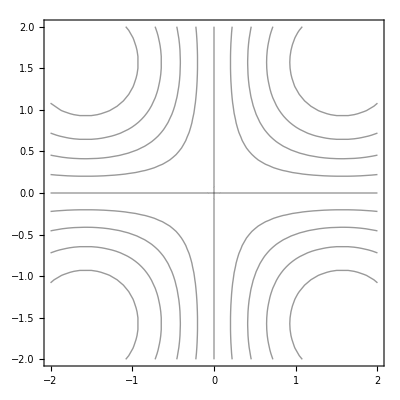

```mathematica
ContourPlot[Sin[x] Sin[y],{x,-2,2},{y,-2,2}]
ContourPlot[Sin[x] Sin[y],{x,-2,2},{y,-2,2},ContourShading->{LightRed,LightPurple}]
ContourPlot[Sin[x] Sin[y],{x,-2,2},{y,-2,2},ContourShading->None] 
(* I suggest going with a minimal color scheme for homework *)
```

### Contours: specifying the values at which to draw contours

This is also an example of using whitespace to make code more readable.

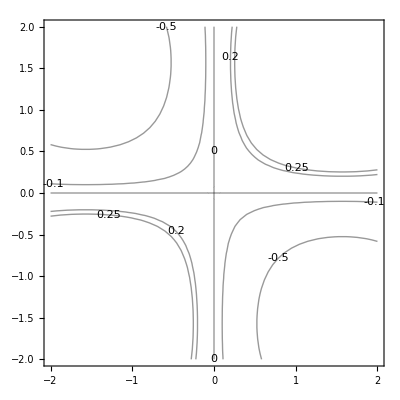

```mathematica
ContourPlot[Sin[x] Sin[y],
{x,-2,2},
{y,-2,2},
Contours->{-.5,-.1,0,.25,.2},
ContourLabels->All,
ContourShading->None
]
```

## Solving equations

### Algebraic Equations

```mathematica
ClearAll["Global`*"]
Solve[x^2+2^2==25,{x}]
```

{{x→-√21},{x→√21}}

### Differential Equations

Interesting ‘fact’: these days young physicists’ first introduction to the special functions (Bessel, Legendre, Hypergeometric, Elliptic...) isn’t in a mathematical physics course, but rather from integrating something difficult in Mathematica.

```mathematica
ClearAll["Global`*"]
DSolve[-p^2 F[z]-D[F[z],{z,2}]+4/z D[F[z],z]+(c^2+c-6)/z^2 F[z]==0,F[z],z]
```

{{F[z]→z^(5/2) BesselJ[1/2 (1+2 c),p z] C[1]+z^(5/2) BesselY[1/2 (1+2 c),p z] C[2]}}

Note that C[1] and C[2] are constants of integration.

## Matrices

Matrices are kind of a pain in the butt. One thing you should remember is to use the dot/period (.) whenever you want to impose matrix multiplication.

### Make matrices look like matrices

You can input matrices using a list of lists and then have them output using the MatrixForm command.

```mathematica
{{a,b},{c,d}}//MatrixForm
```

(a | b
c | d)

### Matrix multiplcation: the wrong way

This does NOT give you a sensible matrix product:

```mathematica
({{a, b}, {c, d}})({{e, f}, {g, h}})//MatrixForm
```

(a e | b f
c g | d h)

### Matrix multiplication: the right way

```mathematica
({{a, b}, {c, d}}).({{e, f}, {g, h}})//MatrixForm
```

(a e+b g | a f+b h
c e+d g | c f+d h)

### Eigensystem, diagonalizing matrices

This returns the matrix eigenvalues and a list of its eigenvectors. This information is packaged as a list whose first item is a list of eigenvalues, the second item is a list of eigenvectors (which are themselves lists).

```mathematica
Eigensystem[({{a, b}, {b, c}})]
```

{{1/2 (a+c-√(a^2+4 b^2-2 a c+c^2)),1/2 (a+c+√(a^2+4 b^2-2 a c+c^2))},{{-(-a+c+√(a^2+4 b^2-2 a c+c^2))/(2 b),1},{-(-a+c-√(a^2+4 b^2-2 a c+c^2))/(2 b),1}}}

From this we can derive the rotation matrix that diagonalizes a matrix:

```mathematica
Rotation=Eigensystem[({{a, b}, {b, c}})][[2]]
Rotation/.{a->1.4,b->2,c->3}//MatrixForm
```

{{-(-a+c+√(a^2+4 b^2-2 a c+c^2))/(2 b),1},{-(-a+c-√(a^2+4 b^2-2 a c+c^2))/(2 b),1}}

(-1.47703 | 1
0.677033 | 1)

Note that the “rotation” matrix is NOT normalized, and somewhat oddly arranged! Let’s check that it actually diagonalizes the matrix. Note that we use the Inverse command rather than just transpose to take care of this odd configuration.

```mathematica
Rotation.({{a, b}, {b, c}}).Inverse[Rotation]/.{a->1.4,b->2,c->3}//MatrixForm
```

(0.0459341 | -5.13478×10^-16
2.22045×10^-16 | 4.35407)

That doesn’t look like it’s diagonal! Well... the off diagonal elements are tiny... but wouldn’t it be nice to make it look prettier? The “chop” command kills things that are really small and probably zero, but non-zero due to numerical accuracy.

```mathematica
Rotation.({{a, b}, {b, c}}).Inverse[Rotation]/.{a->1.4,b->2,c->3}//Chop//MatrixForm
```

(0.0459341 | 0
0 | 4.35407)

## Common Mathematica Techniques

### Get the previous result using %

In general I would avoid using % too much since it depends on the order in which notebook inputs are run.

```mathematica
5+5
%-4
```

10

6

### Decimal points with N

```mathematica
3/4
3/4//N
N[3/4]
```

3/4

0.75

0.75

### Exporting a plot

Once you’ve made a pretty plot, wouldn’t it be great to be able to output it so you can stick it into your LATEX document? Don’t forget to replace the export file path to your OWN path!

```mathematica
FunkyContourPlot=ContourPlot[Sin[x] Sin[y],
{x,-2,2},
{y,-2,2},
Contours->{-.5,-.1,0,.25,.2},
ContourLabels->All,
ContourShading->None
]
```

-Graphics-

```mathematica
Export["/Users/fliptomato/Documents/Teaching/P3327/Section/FunkyContourPlot.pdf",
Show[FunkyContourPlot]
,"PDF"]
```

/Users/fliptomato/Documents/Teaching/P3327/Section/FunkyContourPlot.pdf

Protip: use Insert > File Path to simplify typing in the filename/directory to which you want to export.